## Analytické řešení úlohy kritičnosti heterogenního 1D reaktoru

#### Definice materiálů

```mathematica
dataD:={0.65,0.75,1.15};
Subscript[dataΣ, a]:={0.12,0.10,0.01};
Subscript[dataνΣ, f]:={0.185,0.15,0.00};
```

#### Proud na rozhranní prostředí env1, env2

```mathematica
J[env1_,env2_]:=-Subscript[DD, env1] D[Subscript[ϕ, env1][x],x]/.x->Subscript[ξ, Min[env1,env2],Max[env1,env2]];
```

### Tvar toku ve vnitřní zóně (ϕ_1), vnější zóně (ϕ_2) a reflektoru (ϕ_3)

funkce ϕ_1 zvolena s ohledem na požadavek symetrie v počátku  J(x=0)=0 
funkce ϕ_2 má tvar lineární kombinace trigonometrických funkcí, neboť B_2^2=(νΣ_(f,2)-Σ_(a,2))/D_2>0 
funkce ϕ_3 má tvar lineární kombinace hyperbolických funkcí, neboť B_3^2=(-Σ_(a,3))/D_3<0 
P, Q, R, S 	... integrační konstanty
A 		... normalizační konstanta (určí se např. z podmínky zadaného celkového výkonu reaktoru)

```mathematica
Subscript[ϕ, 1][x_]=A Cos[Subscript[B, 1] x];
Subscript[ϕ, 2][x_]=P Cos[Subscript[B, 2] x]+Q Sin[Subscript[B, 2] x];
Subscript[ϕ, 3][x_]=R Cosh[x/Subscript[L, 3]]+S Sinh[x/Subscript[L, 3]];
```

### Spojitost toku a proudu mezi vnitřní a vnější zónou

```mathematica
c2=FullSimplify[First[Solve[{Subscript[ϕ, 1][Subscript[ξ, 1,2]]==Subscript[ϕ, 2][Subscript[ξ, 1,2]],J[1,2]==J[2,1]},{P,Q}]]]
```

{P→A Cos[B_1 ξ_(1,2)] Cos[B_2 ξ_(1,2)]+(A Sin[B_1 ξ_(1,2)] Sin[B_2 ξ_(1,2)] B_1 DD_1)/(B_2 DD_2),Q→A Cos[B_1 ξ_(1,2)] Sin[B_2 ξ_(1,2)]-(A Cos[B_2 ξ_(1,2)] Sin[B_1 ξ_(1,2)] B_1 DD_1)/(B_2 DD_2)}

```mathematica
Subscript[ϕ, 2][x_]=Subscript[ϕ, 2][x]/.c2//FullSimplify
```

A Cos[B_2 (x-ξ_(1,2))] Cos[B_1 ξ_(1,2)]-(A Sin[B_2 (x-ξ_(1,2))] Sin[B_1 ξ_(1,2)] B_1 DD_1)/(B_2 DD_2)

### Okrajová podmínka vpravo : vakuum na vnějším kraji reflektoru

J-1/2 ϕ==0    v bodě  ξ_r

```mathematica
rbc=FullSimplify[1/2 Subscript[ϕ, 3][Subscript[ξ, r]]+Subscript[DD, 3] D[Subscript[ϕ, 3][x],x]/.x->Subscript[ξ, r]]
```

(Cosh[ξ_r/L_3] (2 S DD_3+R L_3)+Sinh[ξ_r/L_3] (2 R DD_3+S L_3))/(2 L_3)

```mathematica
R3=FullSimplify[First[Solve[rbc==0,R]]]
```

{R→-(S (2 Cosh[ξ_r/L_3] DD_3+Sinh[ξ_r/L_3] L_3))/(2 Sinh[ξ_r/L_3] DD_3+Cosh[ξ_r/L_3] L_3)}

```mathematica
Subscript[ϕ, 3][x_]=Subscript[ϕ, 3][x]/.R3
```

S Sinh[x/L_3]-(S Cosh[x/L_3] (2 Cosh[ξ_r/L_3] DD_3+Sinh[ξ_r/L_3] L_3))/(2 Sinh[ξ_r/L_3] DD_3+Cosh[ξ_r/L_3] L_3)

### Spojitost toku a proudu mezi vnější zónou a reflektorem

```mathematica
c31=Subscript[ϕ, 2][Subscript[ξ, 2,3]]==Subscript[ϕ, 3][Subscript[ξ, 2,3]]
c32=Simplify[J[2,3]==J[3,2]]
```

A Cos[B_1 ξ_(1,2)] Cos[B_2 (-ξ_(1,2)+ξ_(2,3))]-(A Sin[B_1 ξ_(1,2)] Sin[B_2 (-ξ_(1,2)+ξ_(2,3))] B_1 DD_1)/(B_2 DD_2)==S Sinh[(ξ_(2,3))/L_3]-(S Cosh[(ξ_(2,3))/L_3] (2 Cosh[ξ_r/L_3] DD_3+Sinh[ξ_r/L_3] L_3))/(2 Sinh[ξ_r/L_3] DD_3+Cosh[ξ_r/L_3] L_3)

A (Cos[B_2 (-ξ_(1,2)+ξ_(2,3))] Sin[B_1 ξ_(1,2)] B_1 DD_1+Cos[B_1 ξ_(1,2)] Sin[B_2 (-ξ_(1,2)+ξ_(2,3))] B_2 DD_2)==-(S DD_3 (2 Sinh[(ξ_r-ξ_(2,3))/L_3] DD_3+Cosh[(ξ_r-ξ_(2,3))/L_3] L_3))/(L_3 (2 Sinh[ξ_r/L_3] DD_3+Cosh[ξ_r/L_3] L_3))

```mathematica
SS=FullSimplify[First[Solve[c31,S]]]
```

{S→(A (Sin[B_1 ξ_(1,2)] Sin[B_2 (-ξ_(1,2)+ξ_(2,3))] B_1 DD_1-Cos[B_1 ξ_(1,2)] Cos[B_2 (-ξ_(1,2)+ξ_(2,3))] B_2 DD_2) (2 Sinh[ξ_r/L_3] DD_3+Cosh[ξ_r/L_3] L_3))/(B_2 DD_2 (2 Cosh[(ξ_r-ξ_(2,3))/L_3] DD_3+Sinh[(ξ_r-ξ_(2,3))/L_3] L_3))}

```mathematica
Subscript[ϕ, 3][x_]=Subscript[ϕ, 3][x]/.SS
```

(A Sinh[x/L_3] (Sin[B_1 ξ_(1,2)] Sin[B_2 (-ξ_(1,2)+ξ_(2,3))] B_1 DD_1-Cos[B_1 ξ_(1,2)] Cos[B_2 (-ξ_(1,2)+ξ_(2,3))] B_2 DD_2) (2 Sinh[ξ_r/L_3] DD_3+Cosh[ξ_r/L_3] L_3))/(B_2 DD_2 (2 Cosh[(ξ_r-ξ_(2,3))/L_3] DD_3+Sinh[(ξ_r-ξ_(2,3))/L_3] L_3))-(A Cosh[x/L_3] (Sin[B_1 ξ_(1,2)] Sin[B_2 (-ξ_(1,2)+ξ_(2,3))] B_1 DD_1-Cos[B_1 ξ_(1,2)] Cos[B_2 (-ξ_(1,2)+ξ_(2,3))] B_2 DD_2) (2 Cosh[ξ_r/L_3] DD_3+Sinh[ξ_r/L_3] L_3))/(B_2 DD_2 (2 Cosh[(ξ_r-ξ_(2,3))/L_3] DD_3+Sinh[(ξ_r-ξ_(2,3))/L_3] L_3))

Je potřeba zbavit se závislosti na zatím neurčené konstantě A - vzájemným podělením levých a pravých stran

```mathematica
lhs=c32[[1]]/c31[[1]]//FullSimplify
```

(B_2 DD_2 (Cos[B_2 (-ξ_(1,2)+ξ_(2,3))] Sin[B_1 ξ_(1,2)] B_1 DD_1+Cos[B_1 ξ_(1,2)] Sin[B_2 (-ξ_(1,2)+ξ_(2,3))] B_2 DD_2))/(-Sin[B_1 ξ_(1,2)] Sin[B_2 (-ξ_(1,2)+ξ_(2,3))] B_1 DD_1+Cos[B_1 ξ_(1,2)] Cos[B_2 (-ξ_(1,2)+ξ_(2,3))] B_2 DD_2)

```mathematica
rhs=c32[[2]]/c31[[2]]//FullSimplify
```

(DD_3 (2 Sinh[(ξ_r-ξ_(2,3))/L_3] DD_3+Cosh[(ξ_r-ξ_(2,3))/L_3] L_3))/(L_3 (2 Cosh[(ξ_r-ξ_(2,3))/L_3] DD_3+Sinh[(ξ_r-ξ_(2,3))/L_3] L_3))

#### Vstupní data úlohy

fyzikální

```mathematica
DD:=dataD;
Subscript[Σ, a]:=Subscript[dataΣ, a];
Subscript[νΣ, f]:=Subscript[dataνΣ, f];
```

rozhranní jednotlivých zón

```mathematica
Subscript[ξ, 1,2]=50;Subscript[ξ, 2,3]=100;Subscript[ξ, r]=125;
```

#### Definice matematických konstant

```mathematica
L:=√(DD/Subscript[Σ, a]);
B:=√((1/k Subscript[νΣ, f]-Subscript[Σ, a])/DD);
```

#### Dosazení numerických dat do symbolických vzorců

```mathematica
lhsnum=ReplaceAll[lhs,Subscript->Part]
rhsnum=ReplaceAll[rhs,Subscript->Part]
```

(0.866025 √(-0.1+0.15/k) (0.866025 √(-0.1+0.15/k) Cos[62.0174 √(-0.12+0.185/k)] Sin[57.735 √(-0.1+0.15/k)]+0.806226 √(-0.12+0.185/k) Cos[57.735 √(-0.1+0.15/k)] Sin[62.0174 √(-0.12+0.185/k)]))/(0.866025 √(-0.1+0.15/k) Cos[57.735 √(-0.1+0.15/k)] Cos[62.0174 √(-0.12+0.185/k)]-0.806226 √(-0.12+0.185/k) Sin[57.735 √(-0.1+0.15/k)] Sin[62.0174 √(-0.12+0.185/k)])

0.108556

#### Určení kritického čísla k

- je to taková konstanta (stejná pro všechna prostředí), pro niž bude neutronový tok i proud spojitý na rozhranní vnější zóny a reflektoru

Pro všechny hodnoty k_j, v nichž se graf levé strany podmínky spojitosti protíná s grafem pravé strany, je tato podmínka matematicky splněna

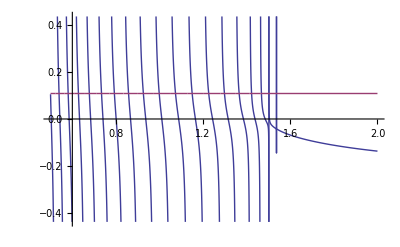

```mathematica
Plot[{lhsnum,rhsnum},{k,0.5,2},Exclusions->{1/lhsnum[[4]]==0},PlotPoints->2000,AxesLabel->{k}]
```

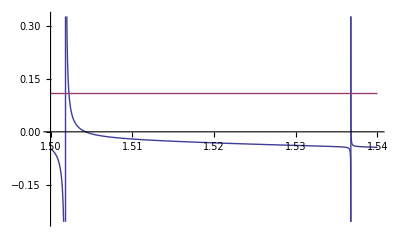

```mathematica
Plot[{lhsnum,rhsnum},{k,1.5,1.54},Exclusions->{{1/lhsnum[[4]]==0},Thread[B<0]},PlotPoints->2000,AxesLabel->{k}]
```

Např. pomocí Newtonovy metody (FindRoot) určíme některé hodnoty k_j

```mathematica
FindRoot[lhsnum-rhsnum,{k,1.537}]
```

{k→1.53675+0. ⅈ}

```mathematica
odhady={0.62,0.73,0.86,1.0,1.15,1.365,1.42,1.46,1.502,1.537};
```

```mathematica
keff=Re[k/.Table[FindRoot[lhsnum-rhsnum,{k,odhady[[i]]}],{i,1,Length[odhady]}]]
```

{0.627999,0.73394,0.857973,0.998686,1.14984,1.36547,1.42249,1.42249,1.50226,1.53675}

### Neutronový tok

```mathematica
Fnum[x_]=ReplaceAll[{Subscript[ϕ, 1][x],Subscript[ϕ, 2][x],Subscript[ϕ, 3][x]},Subscript->Part]
```

{A Cos[1.24035 √(-0.12+0.185/k) x],A Cos[62.0174 √(-0.12+0.185/k)] Cos[1.1547 √(-0.1+0.15/k) (-50+x)]-1/(√(-0.1+0.15/k))0.930949 A √(-0.12+0.185/k) Sin[62.0174 √(-0.12+0.185/k)] Sin[1.1547 √(-0.1+0.15/k) (-50+x)],-1/(√(-0.1+0.15/k))13030.1 A Cosh[0.0932505 x] (-0.866025 √(-0.1+0.15/k) Cos[57.735 √(-0.1+0.15/k)] Cos[62.0174 √(-0.12+0.185/k)]+0.806226 √(-0.12+0.185/k) Sin[57.735 √(-0.1+0.15/k)] Sin[62.0174 √(-0.12+0.185/k)])+1/(√(-0.1+0.15/k))13030.1 A (-0.866025 √(-0.1+0.15/k) Cos[57.735 √(-0.1+0.15/k)] Cos[62.0174 √(-0.12+0.185/k)]+0.806226 √(-0.12+0.185/k) Sin[57.735 √(-0.1+0.15/k)] Sin[62.0174 √(-0.12+0.185/k)]) Sinh[0.0932505 x]}

```mathematica
F123[x_,k_,A_]=Piecewise[{{Fnum[x][[1]], 0≤x≤50}, {Fnum[x][[2]], 50≤x≤100}, {Fnum[x][[3]], 100≤x≤125}}]
```

Piecewise[{{A Cos[1.24035 √(-0.12+0.185/k) x], 0≤x≤50}, {A Cos[62.0174 √(-0.12+0.185/k)] Cos[1.1547 √(-0.1+0.15/k) (-50+x)]-1/(√(-0.1+0.15/k))0.930949 A √(-0.12+0.185/k) Sin[62.0174 √(-0.12+0.185/k)] Sin[1.1547 √(-0.1+0.15/k) (-50+x)], 50≤x≤100}, {-1/(√(-0.1+0.15/k))13030.1 A Cosh[0.0932505 x] (-0.866025 √(-0.1+0.15/k) Cos[57.735 √(-0.1+0.15/k)] Cos[62.0174 √(-0.12+0.185/k)]+0.806226 √(-0.12+0.185/k) Sin[57.735 √(-0.1+0.15/k)] Sin[62.0174 √(-0.12+0.185/k)])+1/(√(-0.1+0.15/k))13030.1 A (-0.866025 √(-0.1+0.15/k) Cos[57.735 √(-0.1+0.15/k)] Cos[62.0174 √(-0.12+0.185/k)]+0.806226 √(-0.12+0.185/k) Sin[57.735 √(-0.1+0.15/k)] Sin[62.0174 √(-0.12+0.185/k)]) Sinh[0.0932505 x], 100≤x≤125}, {0, True}}]

```mathematica
Manipulate[Column[{Plot[F123[x,k,1],{x,0,125},PlotRange->{-0.1,1},PlotPoints->500]}],{{k,keff[[Length[keff]]],"k_eff"},keff}]
```

Pouze poslední průsečík na grafu výše je v takovém bodě k, že příslušný neutronový tok je všude nezáporný => hledané kritické číslo

```mathematica
finkeff=keff[[Length[keff]]]
```

1.53675

### Určení normalizační konstanty na základě požadovaného výkonu v ustáleném stavu

```mathematica
ν=2.43;ϵ=3.204 10^-11;
```

```mathematica
Subscript[P, inner]=ϵ ∫_0^Subscript[ξ, 1,2] 1/finkeff(Subscript[νΣ, f][[1]])/ν F123[x,finkeff,A]ⅆx
Subscript[P, outer]=ϵ ∫_Subscript[ξ, 1,2]^Subscript[ξ, 2,3] 1/finkeff(Subscript[νΣ, f][[2]])/ν F123[x,finkeff,A]ⅆx
```

9.40995×10^-11 A

1.11976×10^-11 A

```mathematica
α=First[Solve[Subscript[P, inner]+Subscript[P, outer]==320,A]]
```

{A→3.03902×10^12}

### Výsledný neutronový tok umožňující dlouhodobě napájet 100W žárovku

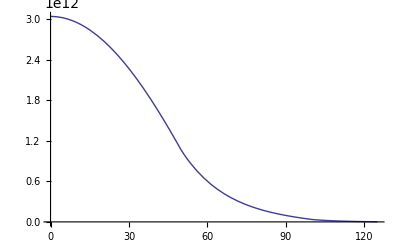

```mathematica
Plot[F123[x,finkeff,A/.α],{x,0,125},PlotRange->{0,A/.α}]
```

```mathematica
xtest=Table[i/10,{i,0,1250}];
ytest=Map[(F123[#,finkeff,A/.α])&,xtest]//Re;
```

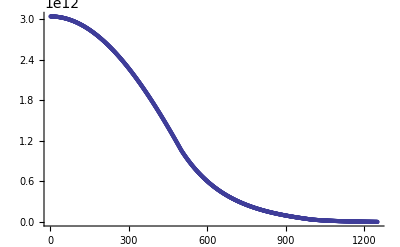

```mathematica
ListPlot[ytest]
```

```mathematica
Export["x.mat", xtest]
```

x.mat

```mathematica
Export["Tok.mat",ytest]
```

Tok.mat

```mathematica
Export["Keff.mat",finkeff]
```

Keff.mat